```mathematica
GraphPlot[Table[Mod[k,Ceiling[k/Pi]]->Mod[3k+RandomInteger[1],Ceiling[k/3]],{k,22500}],ImageSize->1550]
```

```mathematica
10
```

```mathematica
ContourPlot3D[Cos[x]Sin[y]+Cos[y]Sin[z]+Cos[z]Sin[x],{x,-5,5},{y,-5,5},{z,-5,5},Contours->{0},PlotPoints->6,ViewPoint->{1,1,1}]
```

-Graphics3D-

```mathematica
<<Graphics`ContourPlot3D`;
ContourPlot3D[Cos[x]Sin[y]+Cos[y]Sin[z]+Cos[z]Sin[x],{x,-5,5},{y,-5,5},{z,-5,5},Contours->{0},PlotPoints->6,ViewPoint->{1,1,1}]
```

Get::noopen: Cannot open "Graphics`ContourPlot3D`".

-Graphics3D-

```mathematica
<<Graphics`Master`;n=5;r=0.75n;
Twist[{x_,y_,z_},theta_]:={x Cos[theta]-y Sin[theta],x Sin[theta]+y Cos[theta],z};
Warp[{x_,y_,z_},theta_]:={(x+r) Cos[theta],(x+r) Sin[theta],y};
f[z_]:=Module[{t1=Sqrt[2Cot[z]],t2=Cot[z]+1},Warp[Twist[Re[{0.5xsign(Log[t1-t2]-Log[t1+t2])/Sqrt[2],ysign I(ArcTan[1-t1]-ArcTan[1+t1])/Sqrt[2],z}],2Re[z]/n],2Re[z]/n]];
DisplayTogether[Table[ParametricPlot3D[f[x+I y],{x,0,n Pi},{y,0.001,0.75},PlotPoints->{8n+1,5},Compiled->False],{xsign,-1,1,2},{ysign,-1,1,2}]]
```

Get::noopen: Cannot open "Graphics`Master`".

ParametricPlot3D::optx: Unknown option Compiled → False in ParametricPlot3D[f[x + ⅈ\ y], {x, 0, n\ π}, {y, 0.001, 0.75}, PlotPoints → {8\ n + 1, 5}, Compiled → False].

DisplayTogether[{{ParametricPlot3D[f[x+ⅈ y],{x,0,n π},{y,0.001,0.75},PlotPoints→{8 n+1,5},Compiled→False],ParametricPlot3D[f[x+ⅈ y],{x,0,n π},{y,0.001,0.75},PlotPoints→{8 n+1,5},Compiled→False]},{ParametricPlot3D[f[x+ⅈ y],{x,0,n π},{y,0.001,0.75},PlotPoints→{8 n+1,5},Compiled→False],ParametricPlot3D[f[x+ⅈ y],{x,0,n π},{y,0.001,0.75},PlotPoints→{8 n+1,5},Compiled→False]}}]

```mathematica
n=3;ParametricPlot3D[{r Cos[phi]-r^(2n-1) Cos[(2n-1) phi]/(2n-1),r Sin[phi]+r^(2n-1) Sin[(2n-1) phi]/(2n-1),2 r^n Cos[n phi]/n,EdgeForm[]},{phi,0,2Pi},{r,0,1.3},PlotPoints->{181,20},ViewPoint->{0,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
Richmond[n_,z_]:={-1/(2z)-z^(2n+1)/(4n+2),-I/(2z)+I z^(2n+1)/(4n+2),z^n/n};
ParametricPlot3D[Re[Richmond[5,r Exp[I theta]]],{r,0.53,1.187},{theta,0,2Pi},PlotPoints->{25,180},Compiled->False]
```

ParametricPlot3D::optx: Unknown option Compiled → False in ParametricPlot3D[Re[Richmond[5, r\ Exp[ⅈ\ theta]]], {r, 0.53, 1.187}, {theta, 0, 2\ π}, PlotPoints → {25, 180}, Compiled → False].

ParametricPlot3D[Re[Richmond[5,r Exp[ⅈ theta]]],{r,0.53,1.187},{theta,0,2 π},PlotPoints→{25,180},Compiled→False]

```mathematica
G[A_,B_,s_,N_,T_,t_,pr_,th_]:=Graphics[{EdgeForm[{AbsoluteThickness[th],Black}],FaceForm[Pink],Polygon[Table[{{0,0},{(Cos[4a+s*t]+Sin[4a+s*t])Cos[a+s*t],(Cos[4a+s*t]+Sin[4a+s*t]) Sin[a+s*t]},{(Cos[4a+s+s*t]+Sin[4a+s+s*t])Cos[a+s+s*t],(Cos[4a+s+s*t]+Sin[4a+s+s*t]) Sin[a+s+s*t]}},{a,B+T,A+T,2 Pi/N}]]},PlotRange->pr,ImageSize->500]

Manipulate[G[2Pi,0,.75,200,T,0,1.5,.3],{T,0,2Pi}]
```

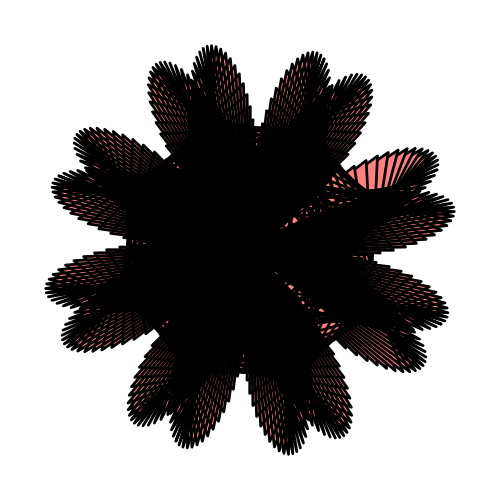

```mathematica
G[2Pi,0,1.75,300,0.055,0.2,1.5,1.97]
```